{{d→InterpolatingFunction[{{0.,1000.}},<>],x→InterpolatingFunction[{{0.,1000.}},<>],m→InterpolatingFunction[{{0.,1000.}},<>],c→InterpolatingFunction[{{0.,1000.}},<>],a→InterpolatingFunction[{{0.,1000.}},<>]}}

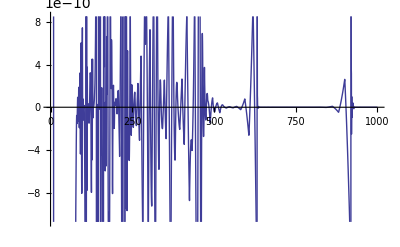

```mathematica
sol1=NDSolve[{d'[t]==.05*d[t]*c[t]*a[t]-.001*x[t]*d[t],x'[t]== 10+.0001*x[t]*c[t]*a[t]-.002*x[t]*d[t],m'[t]==.05*m[t]*c[t]*a[t]-.0005*x[t]*m[t], c'[t]== c[t](1-c[t]),a'[t]== .01*a[t]*(1-a[t]), d[0]==5,x[0]==5,m[0]==1,c[0]==1,a[0]==2},{d,x,m,c,a},{t,0,1000}]

Plot[Evaluate[{d'[t]}/.sol1],{t,0,1000}]
```